```mathematica
lFunc[chevbk_,ch_]:=Module[{a,b, n,z,l},
a=chevbk/ch;
b=(1-chevbk)/(1-ch);
n=a-b;
z=a+b;
l=N[n/z];
Return[l];
];
lApproxFunc[chevbk_,ch_]:=Module[{a,nApprox,zApprox,lApprox},
(* ===== Approximation: b=1 ===== *)
a=chevbk/ch;
nApprox=a-1;
zApprox=a+1;
lApprox=N[nApprox/zApprox];
Return[lApprox];]

lApproxPlotFunc[aInv_]:=Module[{a,nApprox,zApprox,lApprox},
(* ===== Approximation: b=1 ===== *)
a=N[1/aInv];
nApprox=a-1;
zApprox=a+1;
lApprox=N[nApprox/zApprox];
Return[lApprox];]
```

```mathematica
(*LYE/S2 chevbk=0.001211;ch=0.0010311;*)
(*LYE/S4 chevbk=0.00625;ch=0.0010752005672696712;*)
(*LYE/S4.5 chevbk=0.0038314176245210726;ch=0.0006120634711973034;*)
listeS2S4S45={{0.001211,0.0010311},{0.00625,0.0010752005672696712},{0.0038314176245210726,0.0006120634711973034}};
```

```mathematica
Map[Apply[lFunc,listeS2S4S45[[#]]]&,Range[Length[listeS2S4S45]]]
Map[Apply[lApproxFunc,listeS2S4S45[[#]]]&,Range[Length[listeS2S4S45]]]
```

{0.0803267,0.707736,0.725277}

{0.0802373,0.706438,0.724512}

```mathematica
lApproxPlotFunc[0.01]
```

0.980198

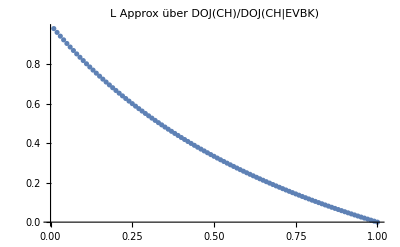

```mathematica
aInv=Table[i,{i,0.01,1,0.01}];
yApprox=Map[lApproxPlotFunc[#]&,aInv];
dataApprox=Map[{aInv[[#]],yApprox[[#]]}&,Range[Length[aInv]]];
lApproxPlot=ListPlot[dataApprox, PlotLabel->"L Approx über DOJ(CH)/DOJ(CH|EVBK)"]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/"];
Export["LApprox.jpeg", lApproxPlot,ImageSize->800, ImageResolution->300]
```

LApprox.jpeg